# ALGORITMO DE BUSQUEDA VORAZ PARA LA OBTENCION DE UN ARBOL EXTENDIDO DE COSTO MINIMO MODIFICADO

# Algoritmo realizado por Jesús Mendoza Verduzco, estudiante de Ing. Sistemas Computacionales del Instituto Tecnológico de Colima.

Datos importados desde “datos.txt”

```mathematica
(*IMPOTAR DATOS*)
datos=Import["/Users/mendo/Desktop/Investigación/datos.txt","Table"];
datos // TableForm
vertices={{0,5000,1},{2500,5000,2},{4000,5000,3},{5000,5000,4},{0,3000,5},{2000,3000,6},{2500,3000,7},{4000,2750,8},{5000,2750,9},{2000,2000,10},{2500,2000,11},{3750,2000,12},{4000,2000,13},{5000,2000,14},{3750,1250,15},{5000,1250,16},{0,500,17},{2000,500,18},{0,0,19},{2000,0,20},{3750,0,21},{5000,0,22}};
aristas={{1,2,2500},{2,3,1500},{3,4,1000},{5,6,2000},{6,7,500},{8,9,1000},{10,11,500},{11,12,1250},{12,13,250},{13,14,1000},{15,16,1250},{17,18,2000},{19,20,2000},{20,21,1750},{21,22,1250},{4,9,2250},{9,14,750},{14,16,750},{16,22,1250},{3,8,2250},{8,13,750},{12,15,750},{15,21,1250},{2,7,2000},{7,11,1000},{6,10,1000},{10,18,1500},{18,20,500},{1,5,2000},{5,17,2500},{17,19,500}};
```

10 | 5000 | 5000 | 
2000 | 3000 | 2500 | 2000
4000 | 2750 | 5000 | 2000
0 | 5000 | 2500 | 3000
2500 | 5000 | 4000 | 2000
4000 | 5000 | 5000 | 2750
2000 | 2000 | 3750 | 0
3750 | 2000 | 5000 | 1250
3750 | 1250 | 5000 | 0
0 | 500 | 2000 | 0
0 | 3000 | 2000 | 500
7 |  |  |

Aristas No Dirigidas, Pesos de Aristas y Coordenadas de Vértices

```mathematica
nEdges=Map[#_⟦1⟧<->#_⟦2⟧&,aristas];
```

```mathematica
eWeigth=Map[#_⟦3⟧&,aristas];
```

```mathematica
coord=Map[Take[#,2]&,vertices];
```

Calculo de Cantidad de Aristas y Pesos de Aristas

```mathematica
Length[nEdges];
Length[eWeigth];
Length[coord];
```

Relación de Aristas con sus Pesos

```mathematica
eEdges=Map[nEdges_⟦#⟧->eWeigth_⟦#⟧&,Range[Length[nEdges]]];
```

Construcción del Grafo a partir de las Aristas, Pesos y  Coordenadas

```mathematica
g=Graph[nEdges,VertexLabels->"Name",VertexSize->Medium,EdgeWeight->eWeigth,VertexCoordinates->coord,EdgeLabels->eEdges];
```

Generación de la lista de polígonos

```mathematica
(*Print["Grafo embebido"]*)
(*coordenadas=GraphEmbedding[g]*)

obtenerListaPoligonos[grafo_,dat_]:=Module[{ g,listaDeVertices,coordenadas,poligonInd,vertice1,vertice2,vertice3,vertice4,coorx1,coorx2,coory1,coory2,
auxiliar,  datos , poligonos},
g=grafo;
datos=dat;
listaDeVertices = VertexList[g];
(*LISTA DE COORDENADAS DE LOS VERTICES DEL GRAFO*)
coordenadas=GraphEmbedding[g];
(*VARIABLES AUXILIARES*)
poligonos={};
vertice1 =0;
(*COORDENADAS DEL VERTICE SUPERIOR IZQUIERDO*)
coorx1=0;
coorx2 =0;
vertice2 =0;
(*COORDENADAS DEL VETICE INFERIOR DERECHO*)
coory1=0;
coory2=0;
vertice3 =0;
vertice4=0;
(*VARIABLE PARA CONSTRUIR EL POLIGONO*)
poligonInd={};
(*AUXILIAR DE VERTICE*)
auxiliar=0;

(*SE RECORREN LAS FILAS DEL ARCHIVO IMPORTADO SALTANDO LA FILA 1*)
For[i=2, i<Length[datos], i++,
(*LA VARIABLE DEL POLIGONO SE LIMPIA*)
poligonInd={};
(*SE DIVIDE EL PROCESO EN DOS, PARA CADA VERTICE EN LA FILA(CADA FILA TIENE 2 VERTICES)*)
For[j=1, j≤ 2, j++,
(*SI ES EL PRIMER CICLO, SE PROCESA EL PRIMER VERTICE*)
If[j==  1,
(*SE OBTIENE EL VERTICE DEL GRAFO QUE CORRESPONDA CON LAS COORDENADAS DADAS EN EL ARCHIVO IMPORTADO*)
vertice1 =Position[coordenadas,{datos[[i]][[1]],datos[[i]][[2]]}][[1]][[1]];
(*SE GUARDAN LAS COORDENADAS DEL VERTICE*)
coorx1 =datos[[i]][[1]];
coory1= datos[[i]][[2]];
,
(*SI ES EL SEGUNDO CICLO, SE PROCESA EL SEGUNDO VERTIDE DE LA FILA DEL ARCHIVO IMPORTADO*)
(*SE GUARDA EL VERTICE*)
vertice2=Position[coordenadas,{datos[[i]][[3]],datos[[i]][[4]]}][[1]][[1]];
(*SE GUARDAN LAS COORDENADAS DEL SEGUNDO EVRTICE*)
coorx2 = datos[[i]][[3]];
coory2= datos[[i]][[4]];
];

];
(*UNA VEZ SE TIENEN LOS VERTICES Y SUS RESPECTIVAS COORDENADAS...*)
(*SE CALCULAN LOS OTROS VERTICES DEL RECTANGULO CON LA MEZCLA DE LAS COORDENADAS DE LOS VERTICES ANTERIORES*)
vertice3 = Position[coordenadas,{coorx1,coory2}][[1]][[1]];
vertice4 = Position[coordenadas,{coorx2,coory1}][[1]][[1]];


(*SE PROCESA EL RECTANGULO PARA ENCONTRAR VERTICES INTERMEDIOS QUE FORMAN PARTE DEL POLIGONO*)
(*EL PROCESO SE REALIZA EN SENTIDO CONTRARIO A LAS MANECILLAS DEL RELOJ, INICIANDO CON EL VERTICE 1, SEGUIDO DEL 3, DEL 4 Y DEL 2*)
(*OBTENER LAS CONEXIONES INTERMEDIAS DE LA HORIZONTAL IZQUIERDA*)
auxiliar = vertice1;
(*SE RECORREN LAS COORDENADAS DE LOS VERTICES DEL GRAFO*)
For[k =1, k≤Length[coordenadas],k++,
(*SI HORIZONTALMENTE SE ENCUENTRA EN LA POSICION DEL PRIMER VERTICE, SE VERIFICA QUE ESTE ENTRE EL VERTICE 1 Y 3*)
If[coordenadas[[k]][[1]]==  coorx1 &&  coordenadas[[k]][[2]]< coory1 && coordenadas[[k]][[2]]>coory2,
(*SE CONECTA ESTE VERTICE CON EL ANTERIOR Y SE AGREGA A LA VARIABLE POLIGONO*)
AppendTo[poligonInd,auxiliar<->k ];
(*EL AUXILIAR SE CONVIERTE EN EL ULTIMO VERTICE*)
auxiliar = k;
]
];
(*SE CONECTA EL ULTIMO VERTICE CON EL VERTICE 3*)
AppendTo[poligonInd,auxiliar<->vertice3];



(*EL PROCESO ANTERIOR SE REPITE EN LOS LADOS RESTANTES*)
(*OBTENER LAS CONEXIONES INTERMEDIAS DE LA VERTICAL INFERIOR*)
auxiliar = vertice3;
For[k =1, k≤Length[coordenadas],k++,
If[coordenadas[[k]][[2]]==  coory2 &&  coordenadas[[k]][[1]]> coorx1 && coordenadas[[k]][[1]]<coorx2,
AppendTo[poligonInd,auxiliar<->k ];
auxiliar = k;
]
];
AppendTo[poligonInd,auxiliar<->vertice2];

(*OBTENER LAS CONEXIONES INTERMEDIAS DE LA HORIZONTAL DERECHA*)
auxiliar = vertice2;
For[k =1, k≤Length[coordenadas],k++,
If[coordenadas[[k]][[1]]==  coorx2 &&  coordenadas[[k]][[2]]< coory1 && coordenadas[[k]][[2]]>coory2,
AppendTo[poligonInd,auxiliar<->k ];
auxiliar = k;
]
];
AppendTo[poligonInd,auxiliar<->vertice4];

(*OBTENER LAS CONEXIONES INTERMEDIAS DE LA VERTICAL SUPERIOR*)
auxiliar = vertice4;
For[k =1, k≤Length[coordenadas],k++,
If[coordenadas[[k]][[2]]==  coory1 &&  coordenadas[[k]][[1]]> coorx1 && coordenadas[[k]][[1]]<coorx2,
AppendTo[poligonInd,auxiliar<->k ];
auxiliar = k;
]
];
AppendTo[poligonInd,auxiliar<->vertice1];
AppendTo[poligonos,poligonInd];
];
(*LA VARIABLE FINAL CONTIENE LA LISTA DE LOS POLIGONOS*)
poligonos
]
```

Obtención de la lista de vertices en la periferia

```mathematica
getListOfPeriferia[v_]:= Module[{vertices,xs,ys,maxX,maxY,verticesPeriferia},
vertices=v;
(*COORDENADAS DE X*)
xs={};
(*COORDENADAS DE Y*)
ys={};
For[x=1,x≤Length[vertices],x++,
AppendTo[xs,vertices[[x]][[1]] ];
AppendTo[ys,vertices[[x]][[2]] ]
];

(*OBTENER LAS COORDENADAS MAYOYES DEL GRAFO; PARA CONOCER LOS LIMITES*)
(*OBTENCION DE LA COORDENADA EN X MAYOR*)
maxX = Max[xs];
(*OBTENCION DE LA COORDENADA EN Y MAYOR*)
maxY = Max[ys];

(*VARIABLE CONTENEDORA DE LOS VERTICES QUE SE ENCUENTREN EN LA PERIFERIA*)
verticesPeriferia= {};
(*SE RECORRE LA LISTA DE VERTICES Y SUS COORDENADAS*)
For[x=1, x≤Length[vertices],x++,
(*SI LA COORDENADA X O Y SE ENCUENTRA EN LOS LÍMITES DEL GRAFO, ES UN VERTICE EN LA PERIFERIA*)
If[vertices[[x]][[1]]== maxX || vertices[[x]][[2]]== maxY || vertices[[x]][[2]]== 0 || vertices[[x]][[1]]== 0 ,
(*SE AGREGA EL VERTICE A LA LISTA DE VERTICES EN LA PERIFERIA*)
AppendTo[verticesPeriferia, vertices[[x]][[3]] ]
];
];
(*VERTICES DE LA PERIFERIA*)
verticesPeriferia
]
```

Algoritmo de Búsqueda Voraz - Estructura de Ciclo

```mathematica
(*Método para la obtención del ciclo más corto, Veriables de entrada: Grafo y vértice raíz*)
greedySearchPath[g_,root_] := Module[{verticePath, verticeGraph, verticeFinal, verticeInicial,  graph, verticeRaiz, verticesPeriferia, poligonos, 
poligonosPath,poligonosGraph, vert, path, aristasGraph, aristasPath, listRandom, longPol, longArGr, 

frontera, listaPath, graphPath,peso},
(*Lista de aristas del grafo*)
aristasGraph = EdgeList[g];
(*Lista de aristas inicializadas para recorrer el camino*)
aristasPath = {};
frontera = 0;
(*Vértice raíz y vertice final*)
verticeRaiz = root;
verticeFinal = 0;
vert = 0;
path = 0;
peso = 0;
graph = g;
(*lista de vértices finales*)
listaPath = {};
(*Llamar el método de la lista de los polígonos ya acomodados*)
poligonos = sortPol[];
(*Lista de los polígonos para recorrer el camino*)
poligonosPath = {};
(*Lista de polígonos que irán restando por el camino*)
poligonosGraph = {};
(*Variable del grafo*)
graphPath = g;
(*Lista de vértices del camino por recorrer*)
verticePath = {};
(*Lista de vértices del grafo*)
verticeGraph = VertexList[g];
(*Llamar la lista de vértices de la periferia por medio de un método*)
verticesPeriferia = getListOfPeriferia[vertices];

(*Solo se ingresa al método si el vértice ingresado en el método es un vértices de la periferia*)
If[MemberQ[verticesPeriferia,verticeRaiz],
(*Se agrega el vértice raíz a la lista de vértices del camino*)
AppendTo[verticePath, verticeRaiz];
(*Se borra el vértice raíz de la lista de vértices del grafo*)
verticeGraph = Delete[verticeGraph, verticeRaiz];
(*Se recorren los polígonos para al igual que el vértice raíz, poder borrarlo en el grafo y agregarlo al camino, solo 
a los polígonos que pertenece el vértice raíz*)
For[i = 1, i≤ Length[poligonos], i++,
p = poligonos[[i]];
vertPol = VertexList[p];
If[MemberQ[vertPol, verticeRaiz],
AppendTo[poligonosPath, p],
AppendTo[poligonosGraph,p];
];
];

(*Vértice raíz toma valor en una variable auxiliar*)
vert = verticeRaiz;
(*Lista final del camino se le agrega el vértice raíz auxiliar*)
AppendTo[listaPath,vert];
(*Se terminará el bucle solo cuando no existan más polígonos en "poligonosGraph"*)
While[Length[poligonosGraph] ≠ 0,
(*Frontera es una variable como resulta de regreso de un método al que se llama
para poder encontrar el camino más corto, se le ingresa los polígonos de camino y los 
restantes del grafo, lo que regresa es la intersección de vértices*)
frontera = fronteras[poligonosGraph, poligonosPath];
(*De la lista de vértices de la frontera, se seleccion por medio de un método el vértice
más corto, o con menor peso, para saber el siguiente recorrido del camino*)
path = selectPath[vert,frontera];

(*Se agrega el nuevo vértice a la lista final del camino*)
AppendTo[listaPath,path];
(*Backtrack solo ocurre en la situación de que no exista ningún camino válido*)
If[path == 0, 
(*Se borra el vértice actual del grafo*)
verticeGraph = Delete[verticeGraph, vert];
(*Se recorren las aristas para poder borrarlas si es que están conectadas al vértice actual*)
For[i=1,i≤ Length[aristasGraph], i++,
e = aristasGraph[[i]];

If[MemberQ[e,vert], 
aristasGraph = Delete[aristasGraph, e];
];
],
(*Si no, si el vertice no ha sido asignado al camino, se agrega y también sus aristas*)
If[!MemberQ[vert,verticePath],
AppendTo[verticePath, vert];
var = vert<->path;
AppendTo[aristasPath, var];
];
];

(*Vértice Auxiliar que en un inicio era el vértice raíz, toma como vértice el nuevo vértice,
sustituyendose para poder seguir con el camino*)
vert = path;
(*Se recorren los polígonos del grafo para agregar los nuevos polígonos al camino y eliminarlos
del grafo*)
For[i = 1, i≤ Length[poligonosGraph], i++,
p = poligonosGraph[[i]];
vertPol = VertexList[p];
If[MemberQ[vertPol,vert],
AppendTo[poligonosPath, p];
poligonosGraph = Delete[poligonosGraph, Position[poligonosGraph,p]];
];
];
];

];
(*Esta parte es de ciclo, lo único que se hace es buscar el camino más corto entre el último vértice y el primero.
Por medio de Dijkstra, y solo si no existe en la lista de vértices final, se agrega*)
pathCiclo = FindShortestPath[g,Last[listaPath],First[listaPath],Method->"Dijkstra"];
For[i = 1,i≤Length[pathCiclo],i++,
If[!MemberQ[listaPath,pathCiclo[[i]]],
AppendTo[listaPath,pathCiclo[[i]]];
];
];

(*Se recorre la lista de vértices final, para destacar el camino en el grafo
y también sacar el peso final del mismo*)
For[i=1,i≤Length[listaPath],i++,
If[Length[listaPath]≥ i+1,
peso = peso + GraphDistance[graph,listaPath[[i]],listaPath[[i+1]]];
];
(*Forma de agregar el peso para cerrar el ciclo*)
If[Length[listaPath]==i,
peso = peso + GraphDistance[graph,Last[listaPath],First[listaPath]];
];
];
graphPath = HighlightGraph[graphPath,Subgraph[graphPath,listaPath]];
(*Se regresan como variables de lista, el grafo destacando el camino más corto
desde el vértice raíz, la lista de vértices final y el peso del camino *)
{graphPath,listaPath, peso}
]
```

Creación de las fronteras

```mathematica
(*Método para la creación de fronteras, se realiza una intersección entre vertices de 2 listas de polígonos*)
fronteras[poligonosGraph_, poligonosPath_] := Module[{grafo, camino, graphLength, pathLength, vertInterseccion},
(*Se inicializan variables y el resultado de la intersección*)
grafo = poligonosGraph;
camino = poligonosPath;
graphLength = Length[grafo];
pathLength = Length[camino];
vertInterseccion= {};
(*La intersección se realiza por medio de los vertices, los que se encuentren en ambas listas de polígonos serán agregados
a una nueva lista de polígonos llamada "vertIntersección"*)

(*Se recorren los vértices de ambas listas en orden y sentido de las manecillas del reloj*)
For [i = 1, i ≤ pathLength, i++,
p = camino[[i]];
vertPath = VertexList[p];
For[j = Length[vertPath],j  ≥ 1, j--,
n = vertPath[[j]];
For[k = 1, k≤ graphLength, k++,
q = grafo[[k]];
vertGraph = VertexList[q];
For[l = Length[vertGraph], l≥1, l--,
m = vertGraph[[l]];
(*Si los vértices son iguales y no ha sido agregado a la lista de "vertIntersección", se agrega*)
If[n == m && !MemberQ[vertInterseccion,m],
AppendTo[vertInterseccion,m];
];
];
];
];
];
(*Se ordena de menor a mayor la lista de vértices para la fácilidad del manejo de la lista*)
vertInterseccion = Sort[vertInterseccion];
(*Se retorna la lista interseccion*)
vertInterseccion
]
```

Selección de Path

```mathematica
(*Método para seleccionar el camino que seguirá en el método principal, seleccionando solo el último vértice de la lista final
Datos de entrada: vértice actual y frontera*)
selectPath[r_,f_] := Module[{pesos, pathing, frontera, root,resultado},
(*Vértice actual*)
root = r;
frontera =f;
(*Lista de pesos*)
pesos = {};
(*Lista de vértieces del vértice más corto*)
pathing = {};

(*Se recorren la lista de vértices de la frontera*)
For[i = 1, i≤Length[frontera],i++,
(*Se saca el peso con el método Dijkstra desde el vértice actual hasta el vértice de la lista de la frontera*)
peso=GraphDistance[g,root,frontera[[i]],Method->"Dijkstra"];
(*Se agrega en la lista de pesos*)
AppendTo[pesos,peso];
(*Se saca el camino más corto con el método Dijkstra desde el vértice actual hasta el vértice de la lista de la frontera*)
path =FindShortestPath[g,root,frontera[[i]], Method->"Dijkstra"];
(*Se agrega en la lista de camino*)
AppendTo[pathing,path];
];
(*Se saca la posición del peso mínimo de la lista de pesos*)
pos = Position[pesos,Min[pesos]][[1]][[1]];
(*Ya que fueron agregados al mismo tiempo, el peso mínimo mantiene la misma posición en la lista de camino que en la lista de pesos*)
resultado = pathing[[pos]];
(*Se selecciona solo el último vértice, ya que lo que devuelve es una conexión de aristas, y se necesita el último vértice recorrido.
Eso es lo que devuelve este método*)
Last[resultado]
]
```

Ordenar polígonos

```mathematica
(*Método para ordenar los polígonos para obtener resultados de una manera más sencilla y el manejo de ellos se facilita.
Este método devuelve una lista de polígonos*)
sortPol[] := Module[{poligonos, newPoligonos},
(*Por medio del método obtenerListaPoligonos, se obtienen los poligonos totales del grafo*)
poligonos = obtenerListaPoligonos[g, datos];
(*Lista de poligonos auxiliar*)
newPoligonos = {};
AppendTo[newPoligonos,poligonos[[3]]];
AppendTo[newPoligonos,poligonos[[4]]];
AppendTo[newPoligonos,poligonos[[5]]];
AppendTo[newPoligonos,poligonos[[10]]];
AppendTo[newPoligonos,poligonos[[1]]];
AppendTo[newPoligonos,poligonos[[2]]];
AppendTo[newPoligonos,poligonos[[9]]];
AppendTo[newPoligonos,poligonos[[6]]];
AppendTo[newPoligonos,poligonos[[7]]];
AppendTo[newPoligonos,poligonos[[8]]];
newPoligonos
]
```

Método para los resultados

```mathematica
(*Este método solo recorre todos los vértices de la periferia, para agregarlos a nueva listas y sacar
el camino con menor peso, su grafo y su lista de vértices*)
Resultado[]:= Module[{listaPesos,listaGrafos,listaPaths,vertPerif,res},
(*Método para encontrar la lista de vértices de la periferia*)
vertPerif = getListOfPeriferia[vertices];
(*Lista de pesos de todos los caminos posibles*)
listaPesos = {};
(*Lista de grafos de todos los caminos posibles*)
listaGrafos = {};
(*Lista de vértices de todos los caminos posibles*)
listaPaths = {};
res={};

(*Camino 1*)
res1 =greedySearchPath[g,vertPerif[[1]]];
AppendTo[listaGrafos,res1[[1]]];
AppendTo[listaPaths,res1[[2]]];
AppendTo[listaPesos,res1[[3]]];
(*Camino 2*)
res2 =greedySearchPath[g,vertPerif[[2]]];
AppendTo[listaGrafos,res2[[1]]];
AppendTo[listaPaths,res2[[2]]];
AppendTo[listaPesos,res2[[3]]];
(*Camino 3*)
res3 =greedySearchPath[g,vertPerif[[3]]];
AppendTo[listaGrafos,res3[[1]]];
AppendTo[listaPaths,res3[[2]]];
AppendTo[listaPesos,res3[[3]]];
(*Camino 4*)
res4 =greedySearchPath[g,vertPerif[[4]]];
AppendTo[listaGrafos,res4[[1]]];
AppendTo[listaPaths,res4[[2]]];
AppendTo[listaPesos,res4[[3]]];
(*Camino 5*)
res5 =greedySearchPath[g,vertPerif[[5]]];
AppendTo[listaGrafos,res5[[1]]];
AppendTo[listaPaths,res5[[2]]];
AppendTo[listaPesos,res5[[3]]];
(*Camino 6*)
res6 =greedySearchPath[g,vertPerif[[6]]];
AppendTo[listaGrafos,res6[[1]]];
AppendTo[listaPaths,res6[[2]]];
AppendTo[listaPesos,res6[[3]]];
(*Camino 7*)
res7 =greedySearchPath[g,vertPerif[[7]]];
AppendTo[listaGrafos,res7[[1]]];
AppendTo[listaPaths,res7[[2]]];
AppendTo[listaPesos,res7[[3]]];
(*Camino 8*)
res8 =greedySearchPath[g,vertPerif[[8]]];
AppendTo[listaGrafos,res8[[1]]];
AppendTo[listaPaths,res8[[2]]];
AppendTo[listaPesos,res8[[3]]];
(*Camino 9*)
res9 =greedySearchPath[g,vertPerif[[9]]];
AppendTo[listaGrafos,res9[[1]]];
AppendTo[listaPaths,res9[[2]]];
AppendTo[listaPesos,res9[[3]]];
(*Camino 10*)
res10 =greedySearchPath[g,vertPerif[[10]]];
AppendTo[listaGrafos,res10[[1]]];
AppendTo[listaPaths,res10[[2]]];
AppendTo[listaPesos,res10[[3]]];
(*Camino 11*)
res11 =greedySearchPath[g,vertPerif[[11]]];
AppendTo[listaGrafos,res11[[1]]];
AppendTo[listaPaths,res11[[2]]];
AppendTo[listaPesos,res11[[3]]];
(*Camino 12*)
res12 =greedySearchPath[g,vertPerif[[12]]];
AppendTo[listaGrafos,res12[[1]]];
AppendTo[listaPaths,res12[[2]]];
AppendTo[listaPesos,res12[[3]]];
(*Camino 13*)
res13 =greedySearchPath[g,vertPerif[[13]]];
AppendTo[listaGrafos,res13[[1]]];
AppendTo[listaPaths,res13[[2]]];
AppendTo[listaPesos,res13[[3]]];

(*Posición del peso mínimo en la lista de pesos*)
pos =Position[listaPesos,Min[listaPesos]][[1]][[1]];
(*Lista de resultados se le agregan el grafo, el peso y lista de vértices del camino más corto
por la posición del peso menor*)
AppendTo[res,listaGrafos[[pos]]];
AppendTo[res,listaPaths[[pos]]];
AppendTo[res,listaPesos[[pos]]];
(*Imprimir las soluciones*)
Print["GRAFO SOLUCIÓN: "];
Print[listaGrafos[[pos]]];
Print["Camino más corto: "];
Print[listaPaths[[pos]]];
Print["Peso total: "];
Print[listaPesos[[pos]]];
(*Se devuelve la lista de resultados del camino más corto*)
res
]
```

Otra Sección

GRAFO SOLUCIÓN:

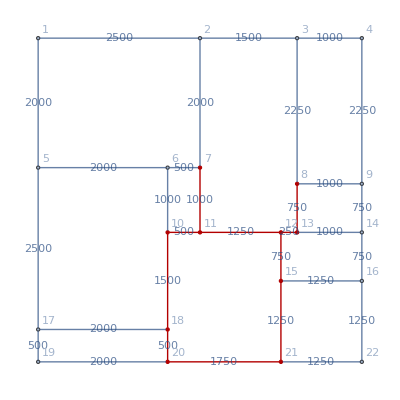

Camino más corto:

{20,18,10,11,7,12,13,8,15,21}

Peso total:

11500.

{1.21875,{-Graphics-,{20,18,10,11,7,12,13,8,15,21},11500.}}

```mathematica
(*Prueba del tiempo de ejecución del Algoritmo de Búsqueda Voraz - Estructura de Ciclo.
El menor tiempo registrado hasta el momento es de 1.21875 segundos.
Un tiempo bastante aceptable considerando que es un camino. Y tambien se considera
que sí es el ciclo más corto como resultado, con un peso de 11500 por el vértice de la periferia número 20.*)
Timing[Resultado[]]
```